```mathematica
-PolyLog[2, -500]
```

-PolyLog[2,-500]

```mathematica
N[-PolyLog[2,-500]]
```

20.9536

```mathematica
E^(PolyLog[ 1, 4*7])
```

-1/27

```mathematica
PolyLog[1,n]
```

-Log[1-n]

```mathematica
E^(-Log[1-4*7])
```

-1/27

```mathematica
Sum[ x^k/(k^1), {k,1,Infinity}]
```

-Log[1-x]

```mathematica
Sum[ x^k/(k^0), {k,1,Infinity}]
```

-x/(-1+x)

```mathematica
Sum[ x^k/(k^2), {k,1,Infinity}]
```

PolyLog[2,x]

```mathematica
Sum[ (-1)^(k+1) x^k/(k^0), {k,1,Infinity}]
```

x/(1+x)

```mathematica
Sum[ (-1)^(k+1) x^k/(k^1), {k,1,Infinity}]
```

Log[1+x]

```mathematica
Sum[ (-1)^(k+1) x^k/(k^2), {k,1,Infinity}]
```

-PolyLog[2,-x]

```mathematica
N[-PolyLog[1,-500]]
```

6.21661

```mathematica
N[Log[1+500]]
```

6.21661

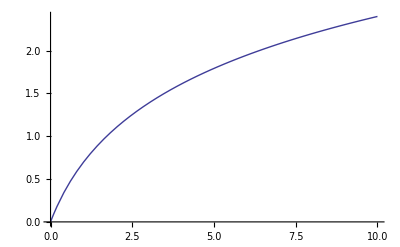

```mathematica
Plot[ -PolyLog[1, -x], {x,0,10}]
```

```mathematica
-PolyLog[1,-500]
```

```mathematica
Sum[ (-1)^(k+1) (x-1)^k/(k^1), {k,1,Infinity}]
```

Log[x]

```mathematica
Sum[ (-1)^(k+1) (( x y )-1)^k/(k^1), {k,1,Infinity}]
```

Log[x y]

```mathematica
-PolyLog[1,1-x]
```

Log[x]

```mathematica
-PolyLog[0,1-x]
```

-(1-x)/x

```mathematica
-PolyLog[0,1-y]
```

-(1-y)/y

```mathematica
-PolyLog[0,1-(x y)]
```

-(1-x y)/(x y)

```mathematica
a+b
```

a+b

```mathematica
E^( -PolyLog[1, 1-(a b)])
```

a b

```mathematica
-PolyLog[1, 1-(a b)]
```

```mathematica
E^Log[a b]
```

a b

```mathematica
E^( -PolyLog[1, 1-a] - PolyLog[1, 1-b])
```

a b

```mathematica
E^( -PolyLog[1, 1-a] - PolyLog[1, 1-b])
```

a b

```mathematica
E^( -PolyLog[0, 1-a] - PolyLog[0, 1-b])
```

ⅇ^(-(1-a)/a-(1-b)/b)

```mathematica
-PolyLog[0, 1-a] - PolyLog[0, 1-b]
```

-(1-a)/a-(1-b)/b

```mathematica
-PolyLog[0, 1-a b]
```

-(1-a b)/(a b)

```mathematica
Log[ E^(a+ b)]
```

Log[ⅇ^(a+b)]

```mathematica
Log[ⅇ^(x+y)]
```

Log[ⅇ^(x+y)]

```mathematica
a b
```

a b

```mathematica
E^( Log[a] + Log[b])
```

a b

```mathematica
coes={1,0.25,0.013888888888888895,0.0017361111111111188,-0.00035879629629629196,0.00014371141975308226,-0.00005917278176703649,0.00002575358606018921,-0.000011678730071493107,0.000005470205591146958,-0.0000026298098586434085,0.0000012916248655325249,-6.458162962094666×10^-7,3.278363479153308×10^-7,-1.6859535517755626  ×10^-7,8.768478486826604×10^-8,-4.605557343857223×10^-8,2.4401456441395295×10^-8,-1.3028809990357962×10^-8,7.0047907395136635×10^-9}
```

{1,0.25,0.0138889,0.00173611,-0.000358796,0.000143711,-0.0000591728,0.0000257536,-0.0000116787,5.47021×10^-6,-2.62981×10^-6,1.29162×10^-6,-6.45816×10^-7,3.27836×10^-7,-1.68595×10^-7,8.76848×10^-8,-4.60556×10^-8,2.44015×10^-8,-1.30288×10^-8,7.00479×10^-9}

```mathematica
{1,0.25,0.013888888888888895,0.0017361111111111188,-0.00035879629629629196,0.00014371141975308226,-0.00005917278176703649,0.00002575358606018921,-0.000011678730071493107,5.470205591146958*^-6,-2.6298098586434085*^-6,1.2916248655325249*^-6,-7-64.58162962094666 x,-7+32.783634791533075 x,-7-16.859535517755624 x,-8+87.68478486826604 x,-8-46.055573438572225 x,-8+24.401456441395297 x,-8-13.028809990357962 x,-9+70.04790739513663 x}
```

{1,0.25,0.0138889,0.00173611,-0.000358796,0.000143711,-0.0000591728,0.0000257536,-0.0000116787,5.47021×10^-6,-2.62981×10^-6,1.29162×10^-6,-7-64.5816 x,-7+32.7836 x,-7-16.8595 x,-8+87.6848 x,-8-46.0556 x,-8+24.4015 x,-8-13.0288 x,-9+70.0479 x}

```mathematica
F[n_]:= Sum[ coes[[k]] n^k, {k,1,20}]
```

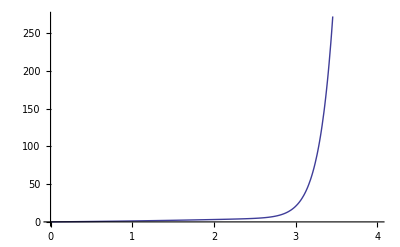

```mathematica
Plot[ F[n], {n,0,4}]
```

```mathematica
coes[[1]]
```

1

```mathematica
cc = Table[2x,{x,1,10}]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
cc(0)
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
coes[[21]]
```

Part::partw: Part 21 of {1, 0.25, 0.0138889, 0.00173611, -0.000358796, 0.000143711, -0.0000591728, « 6 », -7 + 3.27836\ e, -7 - 1.68595\ e, -8 + 8.76848\ e, -8 - 4.60556\ e, -8 + 2.44015\ e, -8 - 1.30288\ e, -9 + 7.00479\ e} does not exist.

{1,0.25,0.0138889,0.00173611,-0.000358796,0.000143711,-0.0000591728,0.0000257536,-0.0000116787,5.47021×10^-6,-2.62981×10^-6,1.29162×10^-6,-7-6.45816 e,-7+3.27836 e,-7-1.68595 e,-8+8.76848 e,-8-4.60556 e,-8+2.44015 e,-8-1.30288 e,-9+7.00479 e}⟦21⟧

```mathematica
F[2]
```

3.13633

```mathematica
N[1/10000000000000000000000000000000]
```

1.×10^-31

```mathematica
F[ -PolyLog[ 2, 1-2]+ -PolyLog[2,1-2] ]
```

2.39338